```mathematica
SetDirectory[NotebookDirectory[]];
CvData = Import["4_cv.dat","Table"];
MagnetData = Import["4_magnetization.dat","Table"];
SusceptData = Import["4_susceptibility.dat","Table"];
```

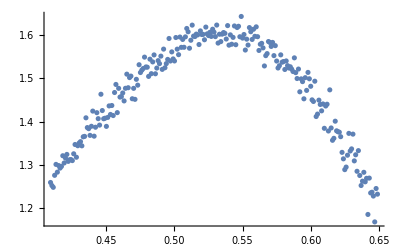

```mathematica
ListPlot[Take[SusceptData,{110, 350}], PlotRange->Full]
```

```mathematica
SusceptFit = NonlinearModelFit[Take[SusceptData,{110,350}],A*Exp[-( x-mu)^2/(2 Sigma^2)],{{A,1.4},Sigma,mu},x];
```

```mathematica
SusceptFit[{"BestFit","ParameterTable"}]
```

{1.60186 ⅇ^(-18.2442 (-0.52851+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 1.60186 | 0.00238576 | 671.427 | 4.7100557005899×10^-392
Sigma | 0.165547 | 0.0011543 | 143.419 | 4.58868×10^-233
mu | 0.52851 | 0.00043997 | 1201.24 | 3.67637472574019×10^-452}

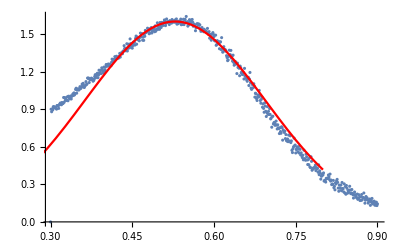

```mathematica
Show[ListPlot[SusceptData, PlotRange->Full],Plot[SusceptFit[x],{x,0,0.8},PlotRange->{{0,0.8},{0,500}}, PlotStyle->Red]]
```

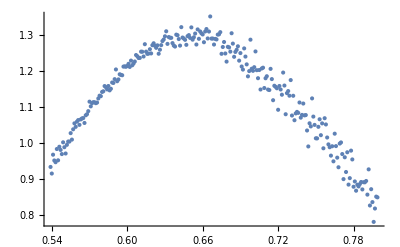

```mathematica
ListPlot[Take[CvData,{240,500}]]
```

```mathematica
CvFit = NonlinearModelFit[Take[CvData,{240,500}],A*Exp[-( x-mu)^2/(2*Sigma^2)],{A,Sigma,mu},x]
```

FittedModel[1.28752 ⅇ^(-22.5018 (-«19»+x)^2)]

```mathematica
CvFit[{"BestFit","ParameterTable"}]
```

{1.28752 ⅇ^(-22.5018 (-0.654407+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 1.28752 | 0.0024789 | 519.393 | 1.39083424254232×10^-391
Sigma | 0.149065 | 0.000986221 | 151.148 | 7.62495×10^-254
mu | 0.654407 | 0.000477986 | 1369.09 | 3.866439814339×10^-500}

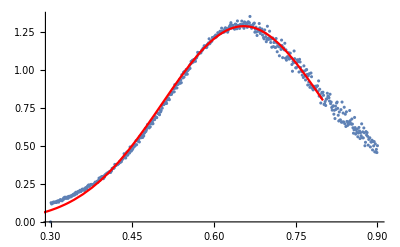

```mathematica
Show[ListPlot[CvData],Plot[CvFit[x],{x,0,0.8},PlotRange->Full,PlotStyle->Red]]
```